## Przypadek pierwszy. Droga opisana równaniem: s[t_]=a1·t^2+a2·t.

### Przypisanie wartości masie oraz parametrom A, B, F. Wprowadzenie wzoru opisującego zależność drogi od czasu.

```mathematica
ClearAll["Global`*"];
```

```mathematica
m=900;        (* kg *)
```

```mathematica
a1=2.3;         (* m/s^2 *)
```

```mathematica
a2=10;            (* m/s *)
```

```mathematica
s[t_]= a1×t^2+a2×t;
```

#### Przedstawienie prędkości "v" jako pierwszej a przyspieszenia "a" jako drugiej pochodnej drogi względem czasu.

```mathematica
v=D[s[t], t]
a=D[s[t], t,t]
```

10+4.6 t

4.6

### Przedstawienie pracy "W" jako całki z iloczynu m·a·v w granicach od zera do czasu t.

```mathematica
W[t_]=∫_0^t a× m ×vⅆt
```

0.+41400. t+9522. t^2

### Sporządzenie wykresów zależności "v", "a" i "W" od czasu.

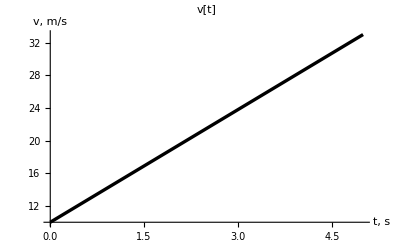

```mathematica
rysv=Plot[v,{t,0,5},
BaseStyle->{FontFamily->"Times", FontSlant->"Italic", FontSize->15},
AxesLabel->{"t, s","v, m/s"},
PlotStyle->{Black,Thickness[0.006]},
PlotLabel->Style["v[t]",
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10]]
```

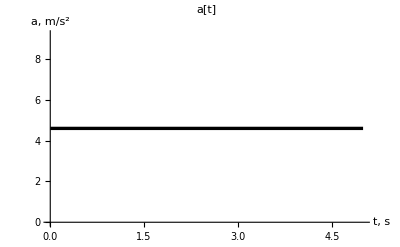

```mathematica
rysa=Plot[a,{t,0,5},
BaseStyle->{FontFamily->"Times", FontSlant->"Italic", FontSize->15},
AxesLabel->{"t, s","a, m/s^2"},
PlotStyle->{Black,Thickness[0.006]},
PlotLabel->Style["a[t]",
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10]]
```

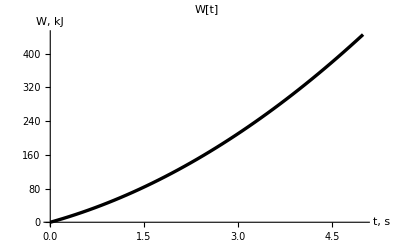

```mathematica
rysw=Plot[W[t]×10^-3,{t,0,5},
BaseStyle->{FontFamily->"Times", FontSlant->"Italic", FontSize->15},
PlotStyle->{Black,Thickness[0.006]},
AxesLabel->{"t, s","W, kJ"},
PlotLabel->Style["W[t]",
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10]]
```

### Obliczenie mocy chwilowej "P".

```mathematica
P=D[W[t], t]
```

41400.+19044. t

### Sporządzenie wykresu zależności "P" od czasu.

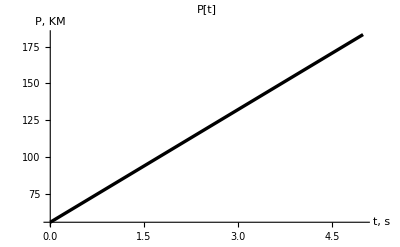

```mathematica
rysw=Plot[P/745.7,{t,0,5},
BaseStyle->{FontFamily->"Times", FontSlant->"Italic", FontSize->15},
PlotStyle->{Black,Thickness[0.006]},
AxesLabel->{"t, s","P, KM"},
PlotLabel->Style["P[t]",
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10]]
```

### Obliczenie mocy średniej "P_sr".

```mathematica
Psr=W[5]/5×1/745.7
```

119.364